## Branching Ratio for Various Models

## Calculating the branching ratio for μ → e + γ, BCW

```mathematica
BrB=Table[0,{i,1,30}];
```

```mathematica
l=1;
While[l<31,{p=0.01;q=5;K=4+l;
cw= Table[0,{x,K+1},{y,K+1}];
(* Dummy matrix to form clockwork mass matrix *)
i=1;
While[i<K+1,{cw[[i+1,i+1]]=1,cw[[i+1,i]]=-q};i++];
i=2;
While[i<K+1,{cw[[i,i+1]]=-q/3};i++];
cw2=cw;cw3=cw;
(* Clockwork mass matrix in Ψ basis, where Ψ = ( Subscript[ψ, L,0],Subscript[ψ, L,1],Subscript[ψ, L,2], ..... Subscript[ψ, L,K-1],Subscript[ψ^c, R,0],Subscript[ψ^c, R,1], .... Subscript[ψ^c, R,K] *)
cw[[1,1]]=p;cw2[[1,1]]=2p;cw3[[1,1]]=3p;
{u1,m1,v1}=SingularValueDecomposition[SetPrecision[cw,50]];{u2,m2,v2}=SingularValueDecomposition[SetPrecision[cw2,50]];{u3,m3,v3}=SingularValueDecomposition[SetPrecision[cw3,50]];
Subscript[M, w] = 0.08;xe1 = Table[0,{i,1,K+1}];xe2 = Table[0,{i,1,K+1}];xe3 = Table[0,{i,1,K+1}];v=0.178;
i=1; While[i<K+2,{xe1[[i]] = Power[m1[[i,i]]/Subscript[M, w],2]};i++];
i=1; While[i<K+2,{xe2[[i]] = Power[m2[[i,i]]/Subscript[M, w],2]};i++];
i=1; While[i<K+2,{xe3[[i]] = Power[m3[[i,i]]/Subscript[M, w],2]};i++];
Fe[x_]:= (10-43*x+78*x^2-49*x^3+4*x^4-18*x^3*Log[x])/(6*Power[1-x,4]);
Fev1 = Table[0,{i,1,K+1}];YM1 = Table[0,{i,1,K+1}];Fev2 = Table[0,{i,1,K+1}];YM2 = Table[0,{i,1,K+1}];Fev3 = Table[0,{i,1,K+1}];YM3 = Table[0,{i,1,K+1}];
i=1;While[i<K+2,{x=xe1[[i]],Fev1[[i]] = N[Fe[x]]};i++];
i=1;While[i<K+2,{YM1[[i]] =u1[[1,i]]*u1[[1,i]]};i++];
i=1;While[i<K+2,{x=xe2[[i]],Fev2[[i]] = N[Fe[x]]};i++];
i=1;While[i<K+2,{YM2[[i]] =u2[[1,i]]*u2[[1,i]]};i++];
i=1;While[i<K+2,{x=xe3[[i]],Fev3[[i]] = N[Fe[x]]};i++];
i=1;While[i<K+2,{YM3[[i]] =u3[[1,i]]*u3[[1,i]]};i++];
YF1 = Sum[YM1[[i]]*Fev1[[i]],{i,1,K+1}];
YF2 = Sum[YM2[[i]]*Fev2[[i]],{i,1,K+1}];
YF3 = Sum[YM3[[i]]*Fev3[[i]],{i,1,K+1}];
Vm = {-0.3001,0.63991,0.671621};
Ve={0.8294,0.5399,-0.1438};
V1=Vm;
V2=Ve;
V1[[-1]]=0.7004224091199636;
V1[[-2]]=0.6475711843516406;
YF = {YF1,YF2,YF3};
YFF = Sum[YF[[i]]*V1[[i]]*V2[[i]],{i,1,3}];
BrB[[l]] = N[3/(8*Pi*137)*YFF^2]};l++]
```

```mathematica
BrB
```

{3.51762×10^-14,1.72442×10^-15,3.08047×10^-15,1.11287×10^-15,1.28346×10^-15,1.11938×10^-15,1.1272×10^-15,1.11553×10^-15,1.11386×10^-15,1.1135×10^-15,1.11301×10^-15,1.11306×10^-15,1.11298×10^-15,1.11299×10^-15,1.11298×10^-15,1.11298×10^-15,1.11298×10^-15,1.11298×10^-15,1.11298×10^-15,1.11298×10^-15,1.11298×10^-15,1.11298×10^-15,1.11298×10^-15,1.11298×10^-15,1.11298×10^-15,1.11298×10^-15,1.11298×10^-15,1.11298×10^-15,1.11298×10^-15,1.11298×10^-15}

```mathematica
cw
```

(0.01 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | -5/3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 1)

## Calculating the branching ratio for μ → e + γ, CNN...

```mathematica
BrCN=Table[0,{i,1,30}];
```

```mathematica
l=1;
While[l<31,{p=0.01;q=5;K=4+l;
cw= Table[0,{x,K+1},{y,K+1}];
(* Dummy matrix to form clockwork mass matrix *)
j=1;
While[j<K+3,{i=1;While[i<K-j+2,{cw[[i+j,i]] = -q};i++]};j++];
i=1;While[i<K+1,{cw[[i+1,i+1]] = 1};i++];
cw2=cw;cw3=cw;
(* Clockwork mass matrix in Ψ basis, where Ψ = ( Subscript[ψ, L,0],Subscript[ψ, L,1],Subscript[ψ, L,2], ..... Subscript[ψ, L,K-1],Subscript[ψ^c, R,0],Subscript[ψ^c, R,1], .... Subscript[ψ^c, R,K] *)
cw[[1,1]]=p;cw2[[1,1]]=2p;cw3[[1,1]]=3p;
{u1,m1,v1}=SingularValueDecomposition[SetPrecision[cw,50]];{u2,m2,v2}=SingularValueDecomposition[SetPrecision[cw2,50]];{u3,m3,v3}=SingularValueDecomposition[SetPrecision[cw3,50]];
Subscript[M, w] = 0.08;xe1 = Table[0,{i,1,K+1}];xe2 = Table[0,{i,1,K+1}];xe3 = Table[0,{i,1,K+1}];v=0.178;
i=1; While[i<K+2,{xe1[[i]] = Power[m1[[i,i]]/Subscript[M, w],2]};i++];
i=1; While[i<K+2,{xe2[[i]] = Power[m2[[i,i]]/Subscript[M, w],2]};i++];
i=1; While[i<K+2,{xe3[[i]] = Power[m3[[i,i]]/Subscript[M, w],2]};i++];
Fe[x_]:= (10-43*x+78*x^2-49*x^3+4*x^4-18*x^3*Log[x])/(6*Power[1-x,4]);
Fev1 = Table[0,{i,1,K+1}];YM1 = Table[0,{i,1,K+1}];Fev2 = Table[0,{i,1,K+1}];YM2 = Table[0,{i,1,K+1}];Fev3 = Table[0,{i,1,K+1}];YM3 = Table[0,{i,1,K+1}];
i=1;While[i<K+2,{x=xe1[[i]],Fev1[[i]] = N[Fe[x]]};i++];
i=1;While[i<K+2,{YM1[[i]] =u1[[1,i]]*u1[[1,i]]};i++];
i=1;While[i<K+2,{x=xe2[[i]],Fev2[[i]] = N[Fe[x]]};i++];
i=1;While[i<K+2,{YM2[[i]] =u2[[1,i]]*u2[[1,i]]};i++];
i=1;While[i<K+2,{x=xe3[[i]],Fev3[[i]] = N[Fe[x]]};i++];
i=1;While[i<K+2,{YM3[[i]] =u3[[1,i]]*u3[[1,i]]};i++];
YF1 = Sum[YM1[[i]]*Fev1[[i]],{i,1,K+1}];
YF2 = Sum[YM2[[i]]*Fev2[[i]],{i,1,K+1}];
YF3 = Sum[YM3[[i]]*Fev3[[i]],{i,1,K+1}];
Vm = {-0.3001,0.63991,0.671621};
Ve={0.8294,0.5399,-0.1438};
V1=Vm;
V2=Ve;
V1[[-1]]=0.7004224091199636;
V1[[-2]]=0.6475711843516406;
YF = {YF1,YF2,YF3};
YFF = Sum[YF[[i]]*V1[[i]]*V2[[i]],{i,1,3}];
BrCN[[l]] = N[3/(8*Pi*137)*YFF^2]};l++]
```

```mathematica
BrCN
```

{4.28228×10^-16,4.28176×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16,4.28174×10^-16}

```mathematica
cw
```

(0.01 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1)

## Calculating the branching ratio for μ → e + γ, GCW

```mathematica
BrG=Table[0,{i,1,30}];
```

```mathematica
l=1;
While[l<30,{p=0.01;q=5;K=4+l;
cw= Table[0,{x,K+1},{y,K+1}];
(* Dummy matrix to form clockwork mass matrix *)
i=2;While[i<K+2,{cw[[i,i]] = 1 };i++];
i=1;While[i<K+1,{cw[[1+i,i]] = -q-(K-i)*0.1};i++];
cw2=cw;cw3=cw;
(* Clockwork mass matrix in Ψ basis, where Ψ = ( Subscript[ψ, L,0],Subscript[ψ, L,1],Subscript[ψ, L,2], ..... Subscript[ψ, L,K-1],Subscript[ψ^c, R,0],Subscript[ψ^c, R,1], .... Subscript[ψ^c, R,K] *)
cw[[1,1]]=p;cw2[[1,1]]=2p;cw3[[1,1]]=3p;
{u1,m1,v1}=SingularValueDecomposition[SetPrecision[cw,50]];{u2,m2,v2}=SingularValueDecomposition[SetPrecision[cw2,50]];{u3,m3,v3}=SingularValueDecomposition[SetPrecision[cw3,50]];
Subscript[M, w] = 0.08;xe1 = Table[0,{i,1,K+1}];xe2 = Table[0,{i,1,K+1}];xe3 = Table[0,{i,1,K+1}];v=0.178;
i=1; While[i<K+2,{xe1[[i]] = Power[m1[[i,i]]/Subscript[M, w],2]};i++];
i=1; While[i<K+2,{xe2[[i]] = Power[m2[[i,i]]/Subscript[M, w],2]};i++];
i=1; While[i<K+2,{xe3[[i]] = Power[m3[[i,i]]/Subscript[M, w],2]};i++];
Fe[x_]:= (10-43*x+78*x^2-49*x^3+4*x^4-18*x^3*Log[x])/(6*Power[1-x,4]);
Fev1 = Table[0,{i,1,K+1}];YM1 = Table[0,{i,1,K+1}];Fev2 = Table[0,{i,1,K+1}];YM2 = Table[0,{i,1,K+1}];Fev3 = Table[0,{i,1,K+1}];YM3 = Table[0,{i,1,K+1}];
i=1;While[i<K+2,{x=xe1[[i]],Fev1[[i]] = N[Fe[x]]};i++];
i=1;While[i<K+2,{YM1[[i]] =u1[[1,i]]*u1[[1,i]]};i++];
i=1;While[i<K+2,{x=xe2[[i]],Fev2[[i]] = N[Fe[x]]};i++];
i=1;While[i<K+2,{YM2[[i]] =u2[[1,i]]*u2[[1,i]]};i++];
i=1;While[i<K+2,{x=xe3[[i]],Fev3[[i]] = N[Fe[x]]};i++];
i=1;While[i<K+2,{YM3[[i]] =u3[[1,i]]*u3[[1,i]]};i++];
YF1 = Sum[YM1[[i]]*Fev1[[i]],{i,1,K+1}];
YF2 = Sum[YM2[[i]]*Fev2[[i]],{i,1,K+1}];
YF3 = Sum[YM3[[i]]*Fev3[[i]],{i,1,K+1}];
Vm = {-0.3001,0.63991,0.671621};
Ve={0.8294,0.5399,-0.1438};
V1=Vm;
V2=Ve;
V1[[-1]]=0.7004224091199636;
V1[[-2]]=0.6475711843516406;
YF = {YF1,YF2,YF3};
YFF = Sum[YF[[i]]*V1[[i]]*V2[[i]],{i,1,3}];
BrG[[l]]=BR = N[3/(8*Pi*137)*YFF^2]};l++]
```

```mathematica
BrG
```

{6.60862×10^-16,6.11948×10^-16,5.67659×10^-16,5.2734×10^-16,4.90562×10^-16,4.56958×10^-16,4.26202×10^-16,3.98007×10^-16,3.7212×10^-16,3.48316×10^-16,3.26397×10^-16,3.06185×10^-16,2.87522×10^-16,2.70267×10^-16,2.54294×10^-16,2.39489×10^-16,2.25752×10^-16,2.1299×10^-16,2.01122×10^-16,1.90073×10^-16,1.79775×10^-16,1.70168×10^-16,1.61198×10^-16,1.52813×10^-16,1.44968×10^-16,1.37622×10^-16,1.30737×10^-16,1.24279×10^-16,1.18217×10^-16,0}

```mathematica
cw
```

(0.01 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-8.2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -8.1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -8. | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -7.9 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -7.8 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -7.7 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -7.6 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -7.5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -7.4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -7.3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -7.2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -7.1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -7. | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6.9 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6.8 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6.7 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6.6 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6.5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6.4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6.3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6.2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6.1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6. | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.9 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.8 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.7 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.6 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.5 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.4 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.3 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.2 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5. | 1)

## Calculating the branching ratio for μ → e + γ, CW

```mathematica
BrC=Table[0,{i,1,30}];
```

```mathematica
l=1;
While[l<31,{p=0.01;q=5;K=4+l;
cw= Table[0,{x,K+1},{y,K+1}];
(* Dummy matrix to form clockwork mass matrix *)
i=2;While[i<K+2,{cw[[i,i]] = 1 };i++];
i=1;While[i<K+1,{cw[[1+i,i]] = -q};i++];
cw2=cw;cw3=cw;
(* Clockwork mass matrix in Ψ basis, where Ψ = ( Subscript[ψ, L,0],Subscript[ψ, L,1],Subscript[ψ, L,2], ..... Subscript[ψ, L,K-1],Subscript[ψ^c, R,0],Subscript[ψ^c, R,1], .... Subscript[ψ^c, R,K] *)
cw[[1,1]]=p;cw2[[1,1]]=2p;cw3[[1,1]]=3p;
{u1,m1,v1}=SingularValueDecomposition[SetPrecision[cw,50]];{u2,m2,v2}=SingularValueDecomposition[SetPrecision[cw2,50]];{u3,m3,v3}=SingularValueDecomposition[SetPrecision[cw3,50]];
Subscript[M, w] = 0.08;xe1 = Table[0,{i,1,K+1}];xe2 = Table[0,{i,1,K+1}];xe3 = Table[0,{i,1,K+1}];v=0.178;
i=1; While[i<K+2,{xe1[[i]] = Power[m1[[i,i]]/Subscript[M, w],2]};i++];
i=1; While[i<K+2,{xe2[[i]] = Power[m2[[i,i]]/Subscript[M, w],2]};i++];
i=1; While[i<K+2,{xe3[[i]] = Power[m3[[i,i]]/Subscript[M, w],2]};i++];
Fe[x_]:= (10-43*x+78*x^2-49*x^3+4*x^4-18*x^3*Log[x])/(6*Power[1-x,4]);
Fev1 = Table[0,{i,1,K+1}];YM1 = Table[0,{i,1,K+1}];Fev2 = Table[0,{i,1,K+1}];YM2 = Table[0,{i,1,K+1}];Fev3 = Table[0,{i,1,K+1}];YM3 = Table[0,{i,1,K+1}];
i=1;While[i<K+2,{x=xe1[[i]],Fev1[[i]] = N[Fe[x]]};i++];
i=1;While[i<K+2,{YM1[[i]] =u1[[1,i]]*u1[[1,i]]};i++];
i=1;While[i<K+2,{x=xe2[[i]],Fev2[[i]] = N[Fe[x]]};i++];
i=1;While[i<K+2,{YM2[[i]] =u2[[1,i]]*u2[[1,i]]};i++];
i=1;While[i<K+2,{x=xe3[[i]],Fev3[[i]] = N[Fe[x]]};i++];
i=1;While[i<K+2,{YM3[[i]] =u3[[1,i]]*u3[[1,i]]};i++];
YF1 = Sum[YM1[[i]]*Fev1[[i]],{i,1,K+1}];
YF2 = Sum[YM2[[i]]*Fev2[[i]],{i,1,K+1}];
YF3 = Sum[YM3[[i]]*Fev3[[i]],{i,1,K+1}];
Vm = {-0.3001,0.63991,0.671621};
Ve={0.8294,0.5399,-0.1438};
V1=Vm;
V2=Ve;
V1[[-1]]=0.7004224091199636;
V1[[-2]]=0.6475711843516406;
YF = {YF1,YF2,YF3};
YFF = Sum[YF[[i]]*V1[[i]]*V2[[i]],{i,1,3}];
BrC[[l]]=BR = N[3/(8*Pi*137)*YFF^2]};l++]
```

```mathematica
BrC
```

{9.09377×10^-16,9.0906×10^-16,9.09047×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16,9.09046×10^-16}

## Calculating the branching ratio for μ → e + γ, CN

```mathematica
BrN=Table[0,{i,1,30}];
```

```mathematica
l=1;
While[l<31,{p=0.01;q=5;K=4+l;q1=5;
cw= Table[0,{x,K+1},{y,K+1}];
(* Dummy matrix to form clockwork mass matrix *)
i=1;
While[i<K+1,{cw[[i+1,i+1]]=1,cw[[i+1,i]]=-q};i++];
i=1;
While[i<K,{cw[[i+2,i]]=-q1};i++];
cw2=cw;cw3=cw;
(* Clockwork mass matrix in Ψ basis, where Ψ = ( Subscript[ψ, L,0],Subscript[ψ, L,1],Subscript[ψ, L,2], ..... Subscript[ψ, L,K-1],Subscript[ψ^c, R,0],Subscript[ψ^c, R,1], .... Subscript[ψ^c, R,K] *)
cw[[1,1]]=p;cw2[[1,1]]=2p;cw3[[1,1]]=3p;
{u1,m1,v1}=SingularValueDecomposition[SetPrecision[cw,50]];{u2,m2,v2}=SingularValueDecomposition[SetPrecision[cw2,50]];{u3,m3,v3}=SingularValueDecomposition[SetPrecision[cw3,50]];
Subscript[M, w] = 0.08;xe1 = Table[0,{i,1,K+1}];xe2 = Table[0,{i,1,K+1}];xe3 = Table[0,{i,1,K+1}];v=0.178;
i=1; While[i<K+2,{xe1[[i]] = SetPrecision[Power[m1[[i,i]]/Subscript[M, w],2],30]};i++];
i=1; While[i<K+2,{xe2[[i]] = SetPrecision[Power[m2[[i,i]]/Subscript[M, w],2],30]};i++];
i=1; While[i<K+2,{xe3[[i]] = SetPrecision[Power[m3[[i,i]]/Subscript[M, w],2],30]};i++];
Fe[x_]:= (10-43*x+78*x^2-49*x^3+4*x^4-18*x^3*Log[x])/(6*Power[1-x,4]);
Fev1 = Table[0,{i,1,K+1}];YM1 = Table[0,{i,1,K+1}];Fev2 = Table[0,{i,1,K+1}];YM2 = Table[0,{i,1,K+1}];Fev3 = Table[0,{i,1,K+1}];YM3 = Table[0,{i,1,K+1}];
i=1;While[i<K+2,{x=xe1[[i]],Fev1[[i]] = N[Fe[x],30]};i++];
i=1;While[i<K+2,{YM1[[i]] =u1[[1,i]]*u1[[1,i]]};i++];
i=1;While[i<K+2,{x=xe2[[i]],Fev2[[i]] = N[Fe[x],30]};i++];
i=1;While[i<K+2,{YM2[[i]] =u2[[1,i]]*u2[[1,i]]};i++];
i=1;While[i<K+2,{x=xe3[[i]],Fev3[[i]] = N[Fe[x],30]};i++];
i=1;While[i<K+2,{YM3[[i]] =u3[[1,i]]*u3[[1,i]]};i++];
YF1 = Sum[YM1[[i]]*Fev1[[i]],{i,1,K+1}];
YF2 = Sum[YM2[[i]]*Fev2[[i]],{i,1,K+1}];
YF3 = Sum[YM3[[i]]*Fev3[[i]],{i,1,K+1}];
Vm = {-0.3001,0.63991,0.671621};
Ve={0.8294,0.5399,-0.1438};
V1=Vm;
V2=Ve;
V1[[-1]]=0.7004224091199636;
V1[[-2]]=0.6475711843516406;
YF = {YF1,YF2,YF3};
YFF = Sum[YF[[i]]*V1[[i]]*V2[[i]],{i,1,3}];
BrN[[l]] = N[3/(8*Pi*137)*YFF^2]};l++]
```

```mathematica
BrN
```

{4.76987×10^-16,4.7731×10^-16,4.77682×10^-16,4.77934×10^-16,4.78115×10^-16,4.78245×10^-16,4.78339×10^-16,4.78406×10^-16,4.78454×10^-16,4.78489×10^-16,4.78514×10^-16,4.78532×10^-16,4.78545×10^-16,4.78554×10^-16,4.78561×10^-16,4.78566×10^-16,4.7857×10^-16,4.78572×10^-16,4.78574×10^-16,4.78576×10^-16,4.78577×10^-16,4.78577×10^-16,4.78578×10^-16,4.78578×10^-16,4.78579×10^-16,4.78579×10^-16,4.78579×10^-16,4.78579×10^-16,4.78579×10^-16,4.78579×10^-16}

```mathematica
cw
```

(0.01 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | -5 | 1)

## Total

```mathematica
BrE = Table[4.2*Power[10,-13],{i,1,30}];
BrE2 = Table[6.0*Power[10,-14],{i,1,30}];
ft = Table[i,{i,30}];
ft2 = Table[{i,i+4},{i,30}];
ft3 =  Table[ft2[[i*5-4]],{i,1,6}];
```

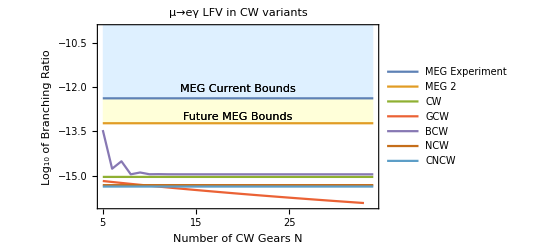

```mathematica
ListLinePlot[Log10[{BrE,BrE2,BrC,BrG,BrB,BrN,BrCN}],Ticks->{ft, Automatic},PlotLegends->LineLegend[{"MEG Experiment","MEG 2","CW","GCW","BCW","NCW","CNCW"},LegendMarkerSize->10,LegendFunction->Frame],Frame->True,PlotLabel->Style["μ→eγ LFV in CW variants",Black],FrameLabel->{"Number of CW Gears N","Log_10 of Branching Ratio"},Filling->{{1->{1,LightBlue}},{2->{-12.4,LightYellow}}},FrameTicks->{{Automatic,None},{ft3,None}},FrameTicksStyle->Directive[Black],AxesOrigin->{1,None},LabelStyle->Directive[Black],PlotRange->{All,{-16,-10}},Epilog->{Text["Future MEG Bounds",Scaled[{0.5,0.50}]] ,Text["Future MEG Bounds",Scaled[{0.5,0.50}]] ,Text["MEG Current Bounds",Scaled[{0.5,0.65}]] ,Text["MEG Current Bounds",Scaled[{0.5,0.65}]] }]
```